```mathematica
ClearAll;
Clear[na];
sel[au_,kl_]:=au[[All,kl]];
(*
Comenzamos con la definicion de ferm, que genera el espacio de Fock para na SP states de un fermion (Dim(H) = 2^na estados puros). No usamos Module, ya que muchas de las definciones las usaremos por fuera del entorno de la funcion
*)
ferm[na_]:=(n=na;
Clear[cm,estado,a,v,mat,au,kel];
(*
Table es un análogo a los list comprehension, iterando con {index, start=1, end, paso=1}. IntegerDigits da una representación en base 2 de k, usando n digitos, en formato de lista. Cada uno de estos, representa un estado puro en el espacio de Fock, con cada posición en la tabla el número de ocupación del SP. De este modo, state corresponde a una base del espacio
*)
state=Table[IntegerDigits[k,2,n],{k,0,2^n-1,1}]; 
(* 
Genera una lista de 2^n elementos ceros, salvo el primero. Usa la misma indexacion que state, de modo que indica cual es el vacio del espacio de Fock en la base state
*)
vacio=Table[If[i==1,1,0],{i,Length[state]}];
(* 
Vamos a crear las matrices de destrucción y creación notadas como cm[i]->Subscript[c, i] y cdm[i]->Subscript[c, i]^†, definidas en 2^n x2^n. Para ello, creamos la funcion auxiliar c(i,m), que, dado el indice del elemento de la base (m), y el nivel SP a desocupar (i), devuelve el indice del estado m con el nivel i desocupado, o 0 si ese nivel estaba desocupado (0 ≠ vacio). Además, este índice cuenta con un signo según la paridad de los niveles ocupados previos al i.
*)
c[i_,m_]:=(st=state[[m]];If[st[[i]]==0,0,(-1)^(Tr[Take[st,i-1]])*(FromDigits[ReplacePart[st,i->0],2]+1)]);
(*
Creamos cada una de las matrices de destrucción iterando con Do sobre los niveles de ocupación (i). Para construir cada una de ellas usamos una SparseArray. Notar que las entradas dt=c[i,m]
{If[dt≠0,Abs[dt],m],m}->Sign[dt]}
Indican que el estado m debe ser enviado a Abs[c[i,m]],   con el signo dado para que las relaciones de conmutación sean las correctas (en particular, las relativas al intercambio de dos fermiones). También creamos los op de creacion, trasponiendo los de destrucción
*)
Do[cm[i]=SparseArray[Join[Table[{m,m}->0,{m,Length[state]}],Table[{dt=c[i,m];If[dt≠0,Abs[dt],m],m}->Sign[dt],{m,Length[state]}]]];
cdm[i]=Transpose[cm[i]],{i,n}]; 
(* Generamos los operadores producto Subscript[c, i]^†Subscript[c, j] Subscript[c, i] Subscript[c, j]^† Subscript[c, i] Subscript[c, j] Subscript[c, i]^†Subscript[c, j]^† *)
Do[cdcm[i,j]=cdm[i].cm[j];ccdm[i,j]=cm[i].cdm[j];ccm[i,j]=cm[i].cm[j];cdcd[i,j]=cdm[i].cdm[j],{i,n},{j,n}]; 
(* 
A continuacion, definimos algunas funciones auxiliares
 *) 
 mf[au_]:=MatrixForm[au]; (* Atajo de MatrixForm *)
indx[au_]:=Flatten[SparseArray[au]["NonzeroPositions"],1];
(* Indica las posiciones de los elementos no nulos de un vector au *)
Do[statex[kel]=Select[state,Tr[#]==kel&];leme[kel]=Length[statex[kel]],{kel,0,n,1}];
(* Selecciona estados con kel fermiones para todo kel (kel es el numero de fermiones), almacenado en statex. Mientras que leme[kel] devuelve en numero de estados con esa cantidad de fermiones *) 
Clear[i,j,m,nuu,au];
(*
Vamos a ver ahora las descomposiciones bipartitas de los estados. Estos corresponden a la matrix Γ del paper definida en la ec 9. i corresponde al índice en el espacio de estados de m fermiones, y j al mismo en nuu-m. au es el estado a descomponer. 
Para la eleccion i,j, si creo un estado no nulo (ax.ay==0), tomo el coeficiente de au asociado a ese estado. Adicionalmente, le pongo un signo para BD.
nuu corresponde al numero de particulas, y au el estado a descomponer
*)
cof[i_,j_,m_,nuu_,au_]:=(ax=statex[m][[i]];axi=indx[ax];ay=statex[nuu-m][[j]];
If[ax.ay==0,au[[iex=FromDigits[ax+ay,2]+1]]*(-1)^(Sum[Tr[Take[ay,axi[[ki]]-1]],{ki,Length[axi]}]),0]);
(* Con los coef de Γ, calculamos la matrix de M cuerpos *)
gamma[m_,nuu_,au_]:= Table[cof[i,j,m,nuu,au],{j,leme[nuu-m]},{i,leme[m]}];
rhomc[m_,nuu_,au_] := gamma[m,nuu,au].Transpose[Conjugate[ gamma[m,nuu,au]]];
rho1c[v_]:=Table[v.cdcm[j,i].v,{i,n},{j,n}];
(* Calcula la matriz densidad de un cuerpo en el estado v*) 
num=Sum[cdcm[i,i],{i,n}]);

(* operador numero de fermiones *)
ssp[mat_]:=(zp=Eigenvalues[mat];a=Select[zp,#>0&&#<1&];If[Length[a]>0,-(a.Log[a]+(1-a).Log[1-a])/Log[2],0]);
(* Calcula la entropia fermionica de una matriz densidad de un cuerpo mat *)  
rev[au_]:=(let=Length[au];
Table[au[[let-i+1,let-j+1]],{i,let},{j,let}]);
(* reversa del orden de estados *)
```

### Ejemplos

```mathematica
ferm[8];
estat=cdm[1].cdm[2].cdm[3].cdm[4].vacio;
{estat.estat,estat.num.estat,estat};
 m=2;nume=4;
rhomc[m, nume, estat] // mf
m=2; nume=4;cmat=Table[cof[i,j,m,nume,estat],{i,leme[m]},{j,leme[nume-m]}];
cmatt=rev[cmat.Transpose[cmat]] // MatrixForm
s=SparseArray[{{1,1}->1,{2,2}->2,{3,3}->3,{1,3}->4}] // mf
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 4
0 | 2 | 0
0 | 0 | 3)

## Hamiltoniano de Pairing

Apliquemos ahora el formalismo anterior para estudiar las descomposiciones y matrices de M cuerpos para estados un poco más interesantes. En este caso, evaluaremos los autoestados del hamiltoniano de Pairing. El mismo, consiste en un término de niveles discretos con degeneración dos (por ejemplo, k y k’), junto con otro término que acopla estos dos niveles, reduciendo la energía. De este modo, esperamos que en el fundamental los estados se den únicamente de a pares. Estudiaremos sistemas de 2n estados y n fermiones (porque es donde se da la física más interesante). Construimos el hamiltoniano para n fermiones:

```mathematica
pairing[n_]:=(nn=n;
it=0;
Clear[xst,xstt,indax];
(* Al igual que en ferm, vamos a representar estados usando vectores binarios, que indican los niveles ocupados. En este
caso, vamos a notarlos como (Subscript[k, 1],Subscript[k, 1]'...), de modo que únicamente nos quedamos con los estados con ambas degeneraciones ocupadas,
ya que esperamos que solo estos contribuyan al fudamental. Más aún, para reducir la dimension del espacio, colapsamos la degeneracion, notando los estados como (Subscript[k, 1],Subscript[k, 2]...=(Subscript[k, 1],Subscript[k, 1]',Subscript[k, 2],Subscript[k, 2]'... *)
(* Construimos los estados al igual que en ferm, y nos quedamos unicamente con los estados con n/2 fermiones, ie, estados = statex[n/2]*)
Table[xstate=IntegerDigits[k,2,nn];If[Tr[xstate]==nn/2,it=it+1;xst[it]=xstate;indax[xstate]=it],{k,0,2^nn-1,1}];
itm=it;
Do[xstl[l]=Table[xst[k][[l]],{k,itm}],{l,nn}];
estados=Table[xst[it],{it,itm}];
(* Construimos la parte de la energia de cada nivel *)
e=1.;
e0=e*Table[k-nn/2-1/2,{k,nn}]; (* Energia de cada modo *)
h0=Table[e0.estados[[i]],{i,itm}]; (* Energia de cada estado *)
h00=DiagonalMatrix[h0]; (* Primera parte del Hamiltoniano *)
(* Ahora vamos a construir el término de interacción. Como la constante es la misma, y estamos sumando sobre todos los operadores,
esta simplemente aporta un término G por cada par de estados que difieren en un modo (es decir, que se obtienen via intercambio de las ocupaciones de k <-> k' *)
Clear[g];
hi=Table[If[estados[[i]].estados[[j]]==nn/2-1,g,0],{i,itm},{j,itm}];
h=h00+hi;
(* Definamos ahora una funcion que nos permite pasar de los estados de esta convencion, a la de ferm.
Primero definimos una funcion auxiliar que asigna a que elemento de la base reducida corresponde a la nueva *)
convelem[au_]:=Module[{s=au,x},
x =Table[0,{i,2Length[s]}];
Do[x[[2i-1]]=s[[i]];
    x[[2i]]=s[[i]];,{i,Length[s]}];
x];
conv[au_]:=Module[{s=au, newCor},
state =Table[IntegerDigits[k,2,2 n],{k,0,2^(2n)-1,1}];
newCor = Table[0,{i,Length[state]}];
Do[idx=Position[state,convelem[estados[[k]]]][[1,1]];
newCor[[idx]]=s[[k]],{k,Length[s]}];
newCor];
)
```

Nos interesa ver el comportamiento de los autovalores de la matriz de M cuerpos, para distintos niveles de energía de h (fundamental, primer excitado...) haciendo un barrido en g. Hasta ahora, con pairing, teníamos definido h

```mathematica
d= 12; (* Dimension del espacio, d | 4 *)
M = 2; (* Grado de la descomposicion, donde 0≤M≤d/2 *)
(* Parametros del barrido *)
gmin = 0.1;
gmax = 10;
gstep = 0.1;
ferm[d];
pairing[d/2];
(* Calculamos autovals y autovect de H, y ordenamos de acuerdo al autovalor. El resultado es una lista de la forma
{{autoval,autovect},...}. Como este fue calculado en un subespacio, lo convertimos al espacio original, y finalmente,
calculamos los autovalores de rho *)
eigenTab =ParallelTable[
{evals,evecs}=Eigensystem[h];
a=SortBy[Transpose[{evals,evecs}],First];
(* El primer indice de a corresponde al nivel, 1 = fundamental, 2 = 1er excitado... 
Adicionalmente, lo convertimos a la base de ferm *)
targState = conv[a[[1]][[2]]];
(* Calculamos los autovalores de la rhom *)
rhomEvals = Eigenvalues[rhomc[M,d/2,targState]],
{g,gmin,gmax,gstep}]
```

{1}
 |  |  |  |

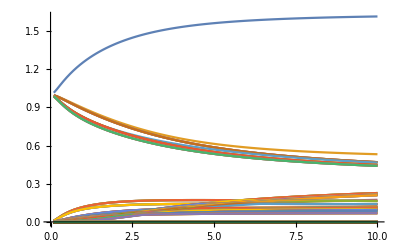

```mathematica
ListLinePlot[Transpose[eigenTab],DataRange->{gmin,gmax},PlotRange->All]
```

```mathematica
d= 12; (* Dimension del espacio, d | 4 *)
M = 2; (* Grado de la descomposicion, donde 0≤M≤d/2 *)
(* Parametros del barrido *)
gmin = 0.1;
gmax = 1;
gstep = 0.1;
ferm[d];
pairing[d/2];
(* Calculamos autovals y autovect de H, y ordenamos de acuerdo al autovalor. El resultado es una lista de la forma
{{autoval,autovect},...}. Como este fue calculado en un subespacio, lo convertimos al espacio original, y finalmente,
calculamos los autovalores de rho *)
g=0.1;
{evals,evecs}=Eigensystem[h];
a=SortBy[Transpose[{evals,evecs}],First];
(* El primer indice de a corresponde al nivel, 1 = fundamental, 2 = 1er excitado... 
Adicionalmente, lo convertimos a la base de ferm *)
targState = conv[a[[1]][[2]]];
(* Calculamos los autovalores de la rhom *)
rhomEvals = Timing[Eigenvalues[rhomc[M,d/2,targState]]]
```

{1.2078,{1.01522,0.995923,0.995346,0.995346,0.995346,0.995346,0.988811,0.988811,0.988811,0.988811,0.988765,0.987343,0.987343,0.987343,0.987343,0.00883618,0.00883618,0.00883618,0.00883618,0.00786676,0.00786676,0.00786676,0.00786676,0.00257392,0.00257392,0.00257392,0.00257392,0.00248197,0.00248197,0.00248197,0.00248197,0.00220973,0.00220973,0.00220973,0.00220973,0.00131989,0.00131989,0.00131989,0.00131989,0.00125682,0.00125682,0.00125682,0.00125682,0.00108936,0.00108936,0.00108936,0.00108936,0.000804745,0.000804745,0.000804745,0.000804745,0.0000765286,0.0000353979,0.0000353979,0.0000353979,0.0000353979,0.0000188869,0.0000188869,0.0000188869,0.0000188869,0.0000106123,6.50827×10^-6,6.50827×10^-6,6.50827×10^-6,6.50827×10^-6,3.01644×10^-6,-2.23634×10^-16,-2.22045×10^-16,2.04115×10^-16,-1.53485×10^-16,-1.39937×10^-16,1.18887×10^-16,-1.18627×10^-16,1.11931×10^-16,-1.11931×10^-16,1.11034×10^-16,1.11014×10^-16,-1.10976×10^-16,1.10257×10^-16,8.75063×10^-17,-8.59186×10^-17,8.18071×10^-17,-7.56495×10^-17,-5.45473×10^-17,5.42381×10^-17,5.16792×10^-17,4.87538×10^-17,-4.5565×10^-17,3.8324×10^-17,3.31131×10^-17,-3.28305×10^-17,-2.89716×10^-17,-2.72403×10^-17,2.72403×10^-17,2.51616×10^-17,2.4463×10^-17,-2.43934×10^-17,2.33252×10^-17,-2.33252×10^-17,-2.33239×10^-17,-2.2961×10^-17,-2.2277×10^-17,2.15869×10^-17,2.07063×10^-17,2.00592×10^-17,-1.96375×10^-17,-1.83021×10^-17,1.83021×10^-17,-1.74246×10^-17,1.74246×10^-17,1.71124×10^-17,-1.69734×10^-17,1.69734×10^-17,1.59948×10^-17,-1.59759×10^-17,1.59759×10^-17,-1.56935×10^-17,-1.47053×10^-17,-1.40138×10^-17,1.40138×10^-17,-1.39763×10^-17,1.38582×10^-17,1.30462×10^-17,-1.23579×10^-17,1.23579×10^-17,-1.22745×10^-17,1.17894×10^-17,-1.16387×10^-17,1.16125×10^-17,-1.11281×10^-17,1.11279×10^-17,-1.11172×10^-17,1.11172×10^-17,-1.09894×10^-17,-1.06687×10^-17,-1.04301×10^-17,1.02027×10^-17,-9.90771×10^-18,9.90771×10^-18,9.89724×10^-18,-9.7799×10^-18,9.50201×10^-18,9.44257×10^-18,-9.44257×10^-18,-9.16946×10^-18,9.00538×10^-18,8.49551×10^-18,-8.18498×10^-18,7.86367×10^-18,-7.83579×10^-18,-7.73646×10^-18,7.73646×10^-18,7.58192×10^-18,-7.58192×10^-18,7.54997×10^-18,7.43203×10^-18,-7.39764×10^-18,7.19356×10^-18,-6.64857×10^-18,6.59501×10^-18,-6.59501×10^-18,6.50709×10^-18,-6.44387×10^-18,6.30926×10^-18,6.02833×10^-18,-5.95256×10^-18,-5.76065×10^-18,-5.56732×10^-18,5.56732×10^-18,-5.45855×10^-18,5.44544×10^-18,5.36714×10^-18,5.16381×10^-18,-5.16381×10^-18,-5.13502×10^-18,5.12357×10^-18,-5.12357×10^-18,5.04142×10^-18,4.91568×10^-18,-4.91568×10^-18,-4.86451×10^-18,-4.82643×10^-18,4.82359×10^-18,4.81563×10^-18,-4.81563×10^-18,-4.57048×10^-18,4.55135×10^-18,-4.48717×10^-18,4.32233×10^-18,4.22306×10^-18,-4.09311×10^-18,4.08071×10^-18,-4.08071×10^-18,-4.0556×10^-18,4.02476×10^-18,3.86581×10^-18,-3.86422×10^-18,-3.78702×10^-18,3.75951×10^-18,-3.63445×10^-18,3.6304×10^-18,3.50177×10^-18,3.49727×10^-18,-3.48411×10^-18,-3.42358×10^-18,-3.37497×10^-18,3.34773×10^-18,3.3204×10^-18,-3.26546×10^-18,-3.17154×10^-18,3.10096×10^-18,-3.08583×10^-18,2.95989×10^-18,2.92649×10^-18,-2.8939×10^-18,2.86756×10^-18,2.85596×10^-18,-2.76136×10^-18,-2.71829×10^-18,-2.69445×10^-18,-2.6672×10^-18,2.62289×10^-18,2.61694×10^-18,2.56435×10^-18,2.53808×10^-18,-2.51973×10^-18,-2.50713×10^-18,2.467×10^-18,-2.40625×10^-18,2.40308×10^-18,-2.31505×10^-18,2.31505×10^-18,-2.2694×10^-18,2.21357×10^-18,-2.21315×10^-18,-2.20071×10^-18,2.20071×10^-18,-2.19236×10^-18,-2.17424×10^-18,2.10711×10^-18,2.04275×10^-18,-2.02213×10^-18,-1.98599×10^-18,1.9616×10^-18,-1.91752×10^-18,1.90701×10^-18,-1.90043×10^-18,-1.88426×10^-18,1.84225×10^-18,-1.79035×10^-18,1.76241×10^-18,-1.72036×10^-18,-1.68869×10^-18,-1.65094×10^-18,1.62621×10^-18,1.61488×10^-18,-1.61488×10^-18,-1.58002×10^-18,1.57756×10^-18,-1.57724×10^-18,1.49837×10^-18,-1.49801×10^-18,-1.481×10^-18,1.4594×10^-18,1.45105×10^-18,-1.36067×10^-18,1.33631×10^-18,1.30398×10^-18,-1.27065×10^-18,1.23824×10^-18,-1.2237×10^-18,1.17811×10^-18,1.15618×10^-18,1.12614×10^-18,-1.09322×10^-18,-1.09151×10^-18,1.0263×10^-18,-1.01509×10^-18,1.00079×10^-18,-1.00012×10^-18,-9.43581×10^-19,-8.94184×10^-19,8.86617×10^-19,-8.62949×10^-19,8.60891×10^-19,-8.53298×10^-19,8.41853×10^-19,8.12951×10^-19,7.5593×10^-19,7.18454×10^-19,-7.16259×10^-19,-7.00483×10^-19,-6.66839×10^-19,6.61386×10^-19,-6.43376×10^-19,6.33853×10^-19,-6.0953×10^-19,5.82689×10^-19,5.65412×10^-19,5.38495×10^-19,5.01813×10^-19,-5.0154×10^-19,4.82397×10^-19,-4.50384×10^-19,-4.08709×10^-19,4.03201×10^-19,-4.01726×10^-19,3.89737×10^-19,-3.53754×10^-19,3.43179×10^-19,-3.34436×10^-19,-3.03261×10^-19,2.95872×10^-19,2.84507×10^-19,-2.83187×10^-19,-2.77544×10^-19,2.6292×10^-19,-2.55076×10^-19,2.19679×10^-19,2.18876×10^-19,-2.18325×10^-19,-2.08698×10^-19,2.06025×10^-19,1.9607×10^-19,-1.7171×10^-19,1.69451×10^-19,-1.46833×10^-19,-1.36254×10^-19,-1.24402×10^-19,1.18468×10^-19,-1.15203×10^-19,9.96703×10^-20,9.10065×10^-20,-8.85323×10^-20,-7.21554×10^-20,-6.44844×10^-20,6.41652×10^-20,6.08831×10^-20,-6.06901×10^-20,-5.18723×10^-20,4.81219×10^-20,-4.08171×10^-20,3.96877×10^-20,3.58602×10^-20,-2.36125×10^-20,-2.15236×10^-20,1.99906×10^-20,1.68023×10^-20,-1.1132×10^-20,1.03191×10^-20,-7.37935×10^-21,-7.1788×10^-21,-4.64122×10^-21,3.98478×10^-21,2.34135×10^-21,-1.65148×10^-21,-6.68103×10^-22,2.02459×10^-25,-2.02459×10^-25,-4.39315×10^-29,4.39313×10^-29,9.14946×10^-33,-8.19358×10^-33,3.48891×10^-33,-2.32103×10^-33,2.2459×10^-33,-1.73508×10^-33,1.58411×10^-33,1.40219×10^-33,-1.20821×10^-33,1.15111×10^-33,-1.10526×10^-33,1.08431×10^-33,-9.93742×10^-34,9.7459×10^-34,-9.19723×10^-34,8.99574×10^-34,-7.79893×10^-34,-6.95325×10^-34,-6.78168×10^-34,6.29104×10^-34,-6.20472×10^-34,6.10112×10^-34,-5.43346×10^-34,5.31527×10^-34,4.7124×10^-34,-4.54026×10^-34,4.40348×10^-34,-4.36105×10^-34,4.24288×10^-34,-3.78409×10^-34,3.65008×10^-34,-3.59917×10^-34,3.51874×10^-34,-3.32799×10^-34,3.29152×10^-34,-3.07938×10^-34,-2.68598×10^-34,2.57111×10^-34,2.38151×10^-34,-2.26093×10^-34,-2.06819×10^-34,1.96541×10^-34,1.79804×10^-34,-1.63756×10^-34,1.19225×10^-34,-1.07958×10^-34,1.02667×10^-34,1.00397×10^-34,-7.60361×10^-35,-6.0836×10^-35,-5.32495×10^-35,4.77263×10^-35,-3.81782×10^-35,-3.46716×10^-35,3.4191×10^-35,-2.73391×10^-35,2.45217×10^-35,2.04723×10^-35,-1.98093×10^-35,1.48955×10^-35,1.36326×10^-35,-1.28372×10^-35,1.175×10^-35,-1.07982×10^-35,1.01156×10^-35,8.57346×10^-36,-8.42114×10^-36,-7.4701×10^-36,-6.43939×10^-36,6.33884×10^-36,5.03061×10^-36,-4.18611×10^-36,3.12164×10^-36,-2.41637×10^-36,1.64274×10^-36,8.3168×10^-37,-7.50262×10^-37,-5.23239×10^-37,2.47293×10^-37,-1.22027×10^-37,4.96048×10^-38,-7.77338×10^-39,5.89999×10^-39,-5.55982×10^-49,-1.00819×10^-49,-8.6303×10^-50,7.93745×10^-50,7.47376×10^-50,-7.25385×10^-50,6.28825×10^-50,-5.2792×10^-50,-4.97519×10^-50,4.64058×10^-50,4.26609×10^-50,3.31015×10^-50,-3.25593×10^-50,-2.97105×10^-50,2.64465×10^-50,-2.5469×10^-50,2.46818×10^-50,1.96575×10^-50,-1.89559×10^-50,1.56781×10^-50,-1.51391×10^-50,-1.32853×10^-50,-1.25718×10^-50,-9.93801×10^-51,8.25617×10^-51,4.8883×10^-51,-4.4959×10^-51,3.46463×10^-51,-3.37015×10^-51,-2.66378×10^-51,1.84462×10^-51,-1.18789×10^-51,7.11507×10^-52,-4.60467×10^-52,-9.83444×10^-53,-2.82186×10^-65,8.74851×10^-66,4.8485×10^-66,-3.99992×10^-66,3.13892×10^-66,-2.78862×10^-66,-2.51835×10^-66,2.2267×10^-66,-1.39889×10^-66,1.15533×10^-66,-9.89083×10^-67,8.39787×10^-67,1.94074×10^-67,1.30189×10^-67,-1.22631×10^-67,4.48384×10^-68}}

```mathematica
Timing[rhomc[M,d/2,targState]]
```

```mathematica
{0.037324,SparseArray[…]}
```

{0.037324,SparseArray[…]}